## Summary

We consider a fixed frequency window defined by 6.1≤p≤15 and a range of mass ratios 10^-9<=ϵ<=1. The main conclusions are:

The current 0PA flux data grid is more than adequate. With a grid of 6.1≤p≤30 in steps of 0.1, the leading PN scaling factored out and 8th order interpolation, it yields an interpolated model with errors ≲10^-10, with the worst case close to the ISCO. A grid with half as many points is about two orders of magnitude less accurate, as expected since 2^8=256≃10^2.

The dephasing from interpolation error is tiny. Over an inspiral from p=15 to p=6.1 the dephasing is ≲10^-5 radians for mass ratio ϵ=10^-6. The dephasing is dominated by the near-ISCO part, so it gets worse for smaller ϵ and better for larger ϵ.

With the default options for NIntegrate the dephasing is dominated by integration error. Over a fixed frequency interval 6.1≤p≤15  the dephasing is ~10^-5/ϵ, so for mass ratio 10^-5 the phase error is order unity.

Setting PrecisionGoal→∞ helps a bit in some cases, but is not the best solution. Keep in mind the definition from Mathematica’s documentation: “With PrecisionGoal->p and AccuracyGoal->a, the Wolfram Language attempts to make the numerical error in a result of size x be less than 10^-a+|x|10^-p.” This means that for x~1$, PrecisionGoal and AccuracyGoal have the same effect. For x≫1 the error is mostly controlled by PrecisionGoal and for x≪1 the error is mostly controlled by AccuracyGoal.  The accumulated phase over a fixed frequency interval is large ~1/ϵ so it is true that PrecisionGoal is controlling the error tolerance. With PrecisionGoal→∞ we have an absolute error tolerance of ~10^-8 (the default value for AccuracyGoal is WorkingPrecision/2), so we are asking for a phase with relative error 10^-8 ϵ. For ϵ≲10^-7 this means we would need to work at greater than machine precision to reach the AccuracyGoal. With Mathematica, this causes it to stop integrating early, once the AccuracyGoal can no longer be met.

There are two problems with accuracy of the numerical integration:

Because of point 3 above, our dephasing is above tolerance (1 radian) for typical EMRI mass ratios.

Because point 4 above we can’t go below a certain mass ratio ϵ≲10^-7.

We can resolve these with two small tweaks:

Rescale the phase by ϵ, i.e. solve for ϵ ϕ_p. This causes the rescaled phase the be 𝒪(1) independently of mass ratio, the same as the other evolved variables (Ω). This change allows us to reach smaller mass ratios without Mathematica aborting the integration early. I think this is similar to, but not quite the same as integrating with respect to slow time.

Use  a higher-than-default setting for PrecisionGoal and AccuracyGoal. With both set to 12, we find a phase accuracy of 10^-8/ϵ, which should be enough for LISA EMRIs. Higher mass ratios will have significant phase error, but they should also involve unreasonably long waveforms that we will never want in actual analysis.

So, in summary, if we use our current  0PA data with the right interpolation and the right integration settings, then everything at 0PA should meet requirements. (Note that this is pretty close  to the settings we used in the waveform letter, a little more accurate but not too much.) There’s no reason to expect new issues related to integration error to arise once we include 1PA, spin effects, etc.

## Load data

### First order fluxes

#### Load data

Load fluxes. These were computed by summing up to l=30, which should be enough to be accurate to machine precision down to the ISCO.

```mathematica
pGrid=;
ℱℰℋdata=;
ℱℰℐdata=;
```

```mathematica
ℱℰℐ[p_]:=Evaluate[32/5 p^-5 Interpolation[Transpose[{pGrid,ℱℰℐdata/(32/5 pGrid^-5)}],InterpolationOrder->8][p]];
```

```mathematica
ℱℰℋ[p_]:=Evaluate[32/5 p^-9 Interpolation[Transpose[{pGrid,ℱℰℋdata/(32/5 pGrid^-9)}],InterpolationOrder->8][p]];
```

```mathematica
ℱℰ[r0_]:=ℱℰℐ[r0]+ℱℰℋ[r0];
```

#### Resample onto uniform-in-y grid and use cubic spline interpolant

```mathematica
With[{ℱℐ=Function[{p},Evaluate[32/5 p^-5 Interpolation[Transpose[{pGrid,ℱℰℐdata/(32/5 pGrid^-5)}],InterpolationOrder->12][p]]],ℱℋ=Function[{p},Evaluate[32/5 p^-9 Interpolation[Transpose[{pGrid,ℱℰℋdata/(32/5 pGrid^-9)}],InterpolationOrder->12][p]]]},
yGrid=(*Subdivide[1/6,1/30,Length[pGrid]]*)Range[1/6,1/30,-0.0005];
ℱℰℐy[p_]:=Evaluate[32/5 p^-5 Interpolation[Transpose[{yGrid,ℱℐ[1/yGrid]/(32/5 yGrid^5)}],Method->"Spline"(*,InterpolationOrder->8*)][1/p]];
ℱℰℋy[p_]:=Evaluate[32/5 p^-9 Interpolation[Transpose[{yGrid,ℱℋ[1/yGrid]/(32/5 yGrid^9)}],Method->"Spline"(*,InterpolationOrder->8*)][1/p]];
]
```

```mathematica
Length/@{yGrid,pGrid}
```

{267,241}

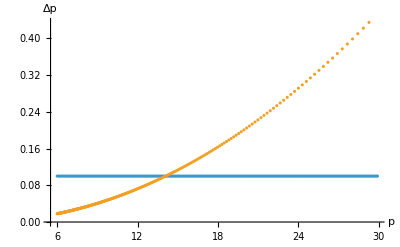

```mathematica
ListPlot[{Transpose[{Most[pGrid],Differences[pGrid]}],Transpose[{Most[1/yGrid],Differences[1/yGrid]}]},PlotRange->All,AxesLabel->{"p","Δp"}]
```

#### Compare against FEW-1PAT1R data

```mathematica
trajectoryFile=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"DataGridChecks","Trajectory1PAT1R.h5"}];
FileHash[trajectoryFile]
```

144710562624649499393268703916386434269

```mathematica
data=Association@@Import[trajectoryFile,"Rules"];
data["StructureGraph"]
```

-Graphics-

```mathematica
data["Datasets"]
```

{/Energy/1PA/Grid,/Energy/1PA/dEdOmega,/Flux/AngularMomentum/0PA/Grid,/Flux/AngularMomentum/0PA/Horizon,/Flux/Energy/0PA/Infinity,/Flux/Energy/0PA/Grid,/Flux/Energy/0PA/Horizon,/Flux/Energy/1PA/Grid,/Flux/Energy/1PA/Infinity,/Flux/Energy/1PAchi1/Grid,/Flux/Energy/1PAchi1/Infinity,/Flux/Energy/1PAchi1/Horizon,/Flux/Energy/1PAchi2/Infinity,/Flux/Energy/1PAchi2/Grid,/Flux/Energy/1PAchi2/Horizon}

#### Check accuracy of interpolants

Validate by trying a less dense grid and a higher order interpolant:

```mathematica
ℱℰℐ2[p_]:=Evaluate[32/5 p^-5 Interpolation[Downsample[Transpose[{pGrid,ℱℰℐdata/(32/5 pGrid^-5)}],{2,1}],InterpolationOrder->8][p]];
```

```mathematica
ℱℰℋ2[p_]:=Evaluate[32/5 p^-9 Interpolation[Downsample[Transpose[{pGrid,ℱℰℋdata/(32/5 pGrid^-9)}],{2,1}],InterpolationOrder->8][p]];
```

```mathematica
ℱℰ2[r0_]:=ℱℰℐ2[r0]+ℱℰℋ2[r0];
```

```mathematica
ℱℰℐ3[p_]:=Evaluate[32/5 p^-5 Interpolation[Transpose[{pGrid,ℱℰℐdata/(32/5 pGrid^-5)}],InterpolationOrder->10][p]];
```

```mathematica
ℱℰℋ3[p_]:=Evaluate[32/5 p^-9 Interpolation[Transpose[{pGrid,ℱℰℋdata/(32/5 pGrid^-9)}],InterpolationOrder->10][p]];
```

```mathematica
ℱℰ3[r0_]:=ℱℰℐ3[r0]+ℱℰℋ3[r0];
```

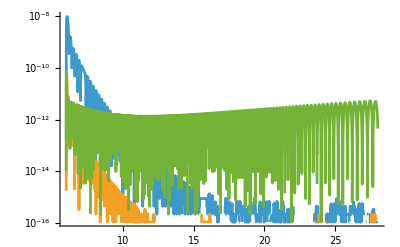

```mathematica
LogPlot[{Abs[1-ℱℰℐ[p]/ℱℰℐ2[p]],Abs[1-ℱℰℐ[p]/ℱℰℐ3[p]],Abs[1-ℱℰℐy[p]/ℱℰℐ3[p]]},{p,6,28},PlotRange->All]
```

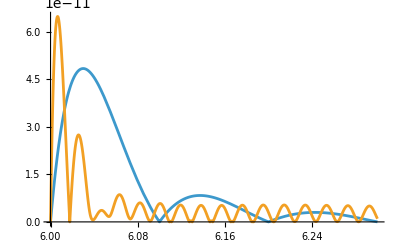

```mathematica
Plot[{Abs[1-ℱℰℐ[p]/ℱℰℐ3[p]],Abs[1-ℱℰℐy[p]/ℱℰℐ3[p]]},{p,6,6.3},PlotRange->All]
```

```mathematica
FindMaximum[{Abs[1-ℱℰℐ[p]/ℱℰℐ3[p]],6<=p<=6.1},p]
```

{1.01594×10^-11,{p→6.08355}}

```mathematica
FindMaximum[{Abs[1-ℱℰℐy[p]/ℱℰℐ3[p]],6<=p<=6.01},p]
```

{6.03448×10^-11,{p→6.00864}}

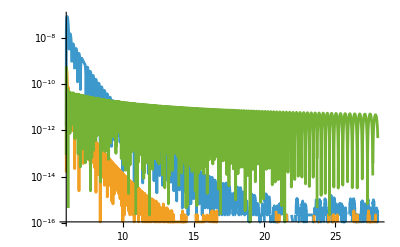

```mathematica
LogPlot[{Abs[1-ℱℰℋ[p]/ℱℰℋ2[p]],Abs[1-ℱℰℋ[p]/ℱℰℋ3[p]],Abs[1-ℱℰℋy[p]/ℱℰℋ3[p]]},{p,6,28},PlotRange->All]
```

So our total fluxes have a precision around 10^-10 at worst. Note the horizon flux has a higher relative error but is smaller in absolute terms than the infinity flux:

```mathematica
ℱℰℋ[6]/ℱℰℐ[6]
```

0.00327434

## 0PA inspiral

```mathematica
M=1;
```

Study a range of mass ratios from ϵ=10^0 to ϵ=10^-10

```mathematica
ϵs=10^(-Range[0,9]);
```

### Standard inspiral and default NDSolve options

```mathematica
Do[{Ωsol[ϵ],ϕsol[ϵ],r0sol[ϵ]}=NDSolveValue[{
Ω'[t]==(3 (1-3 M/r0[t])^(3/2) √(M/r0[t]) ℱℰ[r0[t]] ϵ)/(M^2 (1-6 M/r0[t])), 
ϕ'[t]==Ω[t],
Ω[t]==Sqrt[M/r0[t]^3],
r0[0]==15M,
ϕ[0]==0,
WhenEvent[r0[t]≤6.1M, "StopIntegration"]},{Ω,ϕ,r0},{t,0,∞}];
{tmin[ϵ],tmax[ϵ]}=r0sol[ϵ]["Domain"][[1]];,{ϵ,ϵs}]
```

### Check accuracy

#### Higher accuracy flux data interpolation

```mathematica
Do[{Ωsol3[ϵ],ϕsol3[ϵ],r0sol3[ϵ]}=NDSolveValue[{
Ω'[t]==(3 (1-3 M/r0[t])^(3/2) √(M/r0[t]) ℱℰ3[r0[t]] ϵ)/(M^2 (1-6 M/r0[t])), 
ϕ'[t]==Ω[t],
Ω[t]==Sqrt[M/r0[t]^3],
r0[0]==15M,
ϕ[0]==0,
WhenEvent[r0[t]≤6.1M, "StopIntegration"]},{Ω,ϕ,r0},{t,0,∞}];
{tmin3[ϵ],tmax3[ϵ]}=r0sol3[ϵ]["Domain"][[1]];,{ϵ,ϵs}]
```

```mathematica
GraphicsGrid[Partition[Table[LogPlot[Abs[ϕsol[ϵ][t]-ϕsol3[ϵ][t]],{t,0,Min[tmax[ϵ],tmax3[ϵ]]},PlotStyle->ColorData[116][1-Log10[ϵ]],PlotLabel->StringForm["ϵ = 10^(``)",Log10[ϵ]],PlotTheme->"Detailed",PlotLegends->None],{ϵ,ϵs}],5],ImageSize->2000]
```

```mathematica
GraphicsGrid[Partition[Table[LogPlot[Abs[1-ϕsol[ϵ][t]/ϕsol3[ϵ][t]],{t,0,Min[tmax[ϵ],tmax2[ϵ]]},PlotStyle->ColorData[116][1-Log10[ϵ]],PlotLabel->StringForm["ϵ = 10^(``)",Log10[ϵ]],PlotTheme->"Detailed",PlotLegends->None],{ϵ,ϵs}],5],ImageSize->2000]
```

#### PrecisionGoal=∞

```mathematica
Do[{ΩsolHP[ϵ],ϕsolHP[ϵ],r0solHP[ϵ]}=NDSolveValue[{
Ω'[t]==(3 (1-3 M/r0[t])^(3/2) √(M/r0[t]) ℱℰ[r0[t]] ϵ)/(M^2 (1-6 M/r0[t])), 
ϕ'[t]==Ω[t],
Ω[t]==Sqrt[M/r0[t]^3],
r0[0]==15M,
ϕ[0]==0,
WhenEvent[r0[t]≤6.1M, "StopIntegration"]},{Ω,ϕ,r0},{t,0,∞},PrecisionGoal->∞];
{tminHP[ϵ],tmaxHP[ϵ]}=r0solHP[ϵ]["Domain"][[1]];,{ϵ,ϵs}]
```

```mathematica
(ϕsolHP[10^-7][tmaxHP[10^-7]])/10^(-MachinePrecision/2)
```

```mathematica
Table[{Log10[ϵ],(ϕsolHP[ϵ][tmaxHP[ϵ]])/10^(-MachinePrecision/2),r0solHP[ϵ][tmaxHP[ϵ]]},{ϵ,ϵs}]//Transpose//TableForm
```

This fails for sufficiently small mass ratio ϵ≲10^-7 and long inspiral times. This is because the total phase evolution is large, so that reaching the accuracy goal requires greater than machine precision. Let’s look at the dephasing anyway, but keep in mind that for the smallest three mass ratios we’re not reaching p=6.1.

Dephasing as a function of time

```mathematica
GraphicsGrid[Partition[Table[LogPlot[Abs[ϕsol[ϵ][t]-ϕsolHP[ϵ][t]],{t,0,Min[tmax[ϵ],tmaxHP[ϵ]]},PlotStyle->ColorData[116][1-Log10[ϵ]],PlotLabel->StringForm["ϵ = 10^(``)",Log10[ϵ]],PlotTheme->"Detailed",PlotLegends->None],{ϵ,ϵs}],5],ImageSize->2000]
```

Relative dephasing as a function of time

```mathematica
GraphicsGrid[Partition[Table[LogPlot[Abs[1-ϕsol[ϵ][t]/ϕsolHP[ϵ][t]],{t,0,Min[tmax[ϵ],tmaxHP[ϵ]]},PlotStyle->ColorData[116][1-Log10[ϵ]],PlotLabel->StringForm["ϵ = 10^(``)",Log10[ϵ]],PlotTheme->"Detailed",PlotLegends->None],{ϵ,ϵs}],5],ImageSize->2000]
```

Dephasing as a function of orbital frequency

```mathematica
GraphicsGrid[Partition[Table[ParametricPlot[{Ωsol[ϵ][t],Abs[ϕsol[ϵ][t]-ϕsolHP[ϵ][t]]},{t,0,Min[tmax[ϵ],tmaxHP[ϵ]]},PlotStyle->ColorData[116][1-Log10[ϵ]],PlotLabel->StringForm["ϵ = 10^(``)",Log10[ϵ]],PlotTheme->"Detailed",PlotLegends->None,AspectRatio->1/GoldenRatio,PlotRange->All],{ϵ,ϵs}],5],ImageSize->2000]
```

Dephasing over a fixed frequency interval

```mathematica
GraphicsGrid[{{Show[ListLogLogPlot[Table[{1/ϵ,With[{t=Min[tmax[ϵ],tmaxHP[ϵ]]},ϕsol[ϵ][t]-ϕsolHP[ϵ][t]]},{ϵ,ϵs[[;;-4]]}],PlotTheme->"Detailed",PlotLabel->"Dephasing over fixed frequency interval [15^(-3/2),6.1^(-3/2)]"],LogLogPlot[2 10^-5 q,{q,10^0,10^6}]],
ListLogLogPlot[Table[{1/ϵ,With[{t=Min[tmax[ϵ],tmaxHP[ϵ]]},Abs[1-ϕsol[ϵ][t]/ϕsolHP[ϵ][t]]]},{ϵ,ϵs[[;;-4]]}],PlotTheme->"Detailed",PlotLabel->"Relative dephasing over fixed frequency interval [15^(-3/2),6.1^(-3/2)]"]},{With[{t=Min[tmax[10^0],tmaxHP[10^0]]},ListLogLogPlot[Table[{1/ϵ,Abs[ϕsol[ϵ][t]-ϕsolHP[ϵ][t]]},{ϵ,ϵs[[;;-4]]}],PlotTheme->"Detailed",PlotLabel->"Dephasing over fixed time interval [0, "<>ToString[t]<>"]"]],
With[{t=Min[tmax[10^0],tmaxHP[10^0]]},ListLogLogPlot[Table[{1/ϵ,Abs[1-ϕsol[ϵ][t]/ϕsolHP[ϵ][t]]},{ϵ,ϵs[[;;-4]]}],PlotTheme->"Detailed",PlotLabel->"Relative dephasing over time frequency interval [0, "<>ToString[t]<>"]"]]}},ImageSize->2000]
```

### Try to improve accuracy

#### Evolve ϕ-Ω_0 t with default NDSolve options

```mathematica
Do[{ϕMinusΩ0tsol[ϵ]}=NDSolveValue[{
Ω'[t]==(3 (1-3 M/r0[t])^(3/2) √(M/r0[t]) ℱℰ[r0[t]] ϵ)/(M^2 (1-6 M/r0[t])), 
ϕMinusΩ0t'[t]==Ω[t]-√(M/15^3),
Ω[t]==Sqrt[M/r0[t]^3],
r0[0]==15M,
ϕMinusΩ0t[0]==0,
WhenEvent[r0[t]≤6.1M, "StopIntegration"]},{ϕMinusΩ0t},{t,0,∞}];,{ϵ,10^(-Range[0,10])}]
```

```mathematica
Do[{ϕMinusΩ0tMinusΩ0primet2sol[ϵ]}=NDSolveValue[{
Ω'[t]==(3 (1-3 M/r0[t])^(3/2) √(M/r0[t]) ℱℰ[r0[t]] ϵ)/(M^2 (1-6 M/r0[t])), 
ϕMinusΩ0tMinusΩ0primet2'[t]==Ω[t]-(√(M/15^3)+(3 (1-3 M/15)^(3/2) √(M/15) ℱℰ[15] ϵ)/(M^2 (1-6 M/15))t),
Ω[t]==Sqrt[M/r0[t]^3],
r0[0]==15M,
ϕMinusΩ0tMinusΩ0primet2[0]==0,
WhenEvent[r0[t]≤6.1M, "StopIntegration"]},{ϕMinusΩ0tMinusΩ0primet2},{t,0,∞}];,{ϵ,10^(-Range[0,10])}]
```

```mathematica
LogPlot[Evaluate[Abs@{ϕsol[10^-5][t],ϕMinusΩ0tsol[10^-5][t],ϕMinusΩ0tMinusΩ0primet2solHP[10^-5][t]}],{t,0,tmax[10^-5]}]
```

```mathematica
With[{ϵ=10^-5},LogPlot[{ϕsol[ϵ][t]-ϕsolHP[ϵ][t],Abs[ϕMinusΩ0tsol[ϵ][t]+√(M/15^3)t-ϕsolHP[ϵ][t]],Abs[ϕMinusΩ0tMinusΩ0primet2sol[ϵ][t]+√(M/15^3)t+1/2(3 (1-3 M/15)^(3/2) √(M/15) ℱℰ[15] ϵ)/(M^2 (1-6 M/15))t^2-ϕsolHP[ϵ][t]]},{t,0,tmax[ϵ]}]]
```

#### Evolve ϕ-Ω t with default NDSolve options

```mathematica
Do[{ϕMinusΩtsol[ϵ]}=NDSolveValue[{
Ω'[t]==(3 (1-3 M/r0[t])^(3/2) √(M/r0[t]) ℱℰ[r0[t]] ϵ)/(M^2 (1-6 M/r0[t])), 
ϕMinusΩt'[t]==-Ω'[t]t,
Ω[t]==Sqrt[M/r0[t]^3],
r0[0]==15M,
ϕMinusΩt[0]==0,
WhenEvent[r0[t]≤6.1M, "StopIntegration"]},{ϕMinusΩt},{t,0,∞}];,{ϵ,10^(-Range[0,10])}]
```

#### Scale ϕ by ϵ - this allows us to reach higher mass ratios/integration times, but doesn’t change the fundamental accuracy

```mathematica
Do[{Ωϵsol[ϵ],ϕϵsol[ϵ],r0ϵsol[ϵ]}=NDSolveValue[{
Ω'[t]==(3 (1-3 M/r0[t])^(3/2) √(M/r0[t]) ℱℰ[r0[t]] ϵ)/(M^2 (1-6 M/r0[t])), 
ϕ'[t]==Ω[t]ϵ,
Ω[t]==Sqrt[M/r0[t]^3],
r0[0]==15M,
ϕ[0]==0,
WhenEvent[r0[t]≤6.1M, "StopIntegration"]},{Ω,ϕ,r0},{t,0,∞}];
{tminϵ[ϵ],tmaxϵ[ϵ]}=r0sol[ϵ]["Domain"][[1]];,{ϵ,ϵs}]
```

```mathematica
Do[{ΩϵsolHP[ϵ],ϕϵsolHP[ϵ],r0ϵsolHP[ϵ]}=NDSolveValue[{
Ω'[t]==(3 (1-3 M/r0[t])^(3/2) √(M/r0[t]) ℱℰ[r0[t]] ϵ)/(M^2 (1-6 M/r0[t])), 
ϕ'[t]==Ω[t]ϵ,
Ω[t]==Sqrt[M/r0[t]^3],
r0[0]==15M,
ϕ[0]==0,
WhenEvent[r0[t]≤6.1M, "StopIntegration"]},{Ω,ϕ,r0},{t,0,∞},PrecisionGoal->13,AccuracyGoal->13];
{tminϵHP[ϵ],tmaxϵHP[ϵ]}=r0sol[ϵ]["Domain"][[1]];,{ϵ,ϵs}]
```

Dephasing as a function of time

```mathematica
GraphicsGrid[Partition[Table[LogPlot[Abs[(ϕϵsol[ϵ][t])/ϵ-(ϕϵsolHP[ϵ][t])/ϵ],{t,0,Min[tmaxϵ[ϵ],tmaxϵHP[ϵ]]},PlotStyle->ColorData[116][1-Log10[ϵ]],PlotLabel->StringForm["ϵ = 10^(``)",Log10[ϵ]],PlotTheme->"Detailed",PlotLegends->None],{ϵ,ϵs}],5],ImageSize->2000]
```

Relative dephasing as a function of time

```mathematica
GraphicsGrid[Partition[Table[LogPlot[Abs[1-(ϕϵsol[ϵ][t]/ϵ)/(ϕϵsolHP[ϵ][t]/ϵ)],{t,0,Min[tmaxϵ[ϵ],tmaxϵHP[ϵ]]},PlotStyle->ColorData[116][1-Log10[ϵ]],PlotLabel->StringForm["ϵ = 10^(``)",Log10[ϵ]],PlotTheme->"Detailed",PlotLegends->None],{ϵ,ϵs}],5],ImageSize->2000]
```

Dephasing as a function of orbital frequency

```mathematica
GraphicsGrid[Partition[Table[ParametricPlot[{Ωϵsol[ϵ][t],Abs[ϕϵsol[ϵ][t]/ϵ-ϕϵsolHP[ϵ][t]/ϵ]},{t,0,Min[tmaxϵ[ϵ],tmaxϵHP[ϵ]]},PlotStyle->ColorData[116][1-Log10[ϵ]],PlotLabel->StringForm["ϵ = 10^(``)",Log10[ϵ]],PlotTheme->"Detailed",PlotLegends->None,AspectRatio->1/GoldenRatio,PlotRange->All],{ϵ,ϵs}],5],ImageSize->2000]
```

Dephasing over a fixed frequency interval

```mathematica
GraphicsGrid[{{Show[ListLogLogPlot[Table[{1/ϵ,With[{t=Min[tmaxϵ[ϵ],tmaxϵHP[ϵ]]},ϕϵsol[ϵ][t]/ϵ-ϕϵsolHP[ϵ][t]/ϵ]},{ϵ,ϵs}],PlotTheme->"Detailed",PlotLabel->"Dephasing over fixed frequency interval [15^(-3/2),6.1^(-3/2)]"],LogLogPlot[2 10^-5 q,{q,10^0,10^9}]],
ListLogLogPlot[Table[{1/ϵ,With[{t=Min[tmaxϵ[ϵ],tmaxϵHP[ϵ]]},Abs[1-(ϕϵsol[ϵ][t]/ϵ)/(ϕϵsolHP[ϵ][t]/ϵ)]]},{ϵ,ϵs}],PlotTheme->"Detailed",PlotLabel->"Relative dephasing over fixed frequency interval [15^(-3/2),6.1^(-3/2)]"]},{With[{t=Min[tmaxϵ[10^0],tmaxϵHP[10^0]]},ListLogLogPlot[Table[{1/ϵ,Abs[ϕϵsol[ϵ][t]/ϵ-ϕϵsolHP[ϵ][t]/ϵ]},{ϵ,ϵs}],PlotTheme->"Detailed",PlotLabel->"Dephasing over fixed time interval [0, "<>ToString[t]<>"]"]],
With[{t=Min[tmaxϵ[10^0],tmaxϵHP[10^0]]},ListLogLogPlot[Table[{1/ϵ,Abs[1-(ϕϵsol[ϵ][t]/ϵ)/(ϕϵsolHP[ϵ][t]/ϵ)]},{ϵ,ϵs}],PlotTheme->"Detailed",PlotLabel->"Relative dephasing over time frequency interval [0, "<>ToString[t]<>"]"]]}},ImageSize->2000]
```

#### Scale ϕ by ϵ and increase PrecisionGoal and AccuracyGoal - this decreases phase error

```mathematica
Do[{ΩϵsolPG12[ϵ],ϕϵsolPG12[ϵ],r0ϵsolPG12[ϵ]}=NDSolveValue[{
Ω'[t]==(3 (1-3 M/r0[t])^(3/2) √(M/r0[t]) ℱℰ[r0[t]] ϵ)/(M^2 (1-6 M/r0[t])), 
ϕ'[t]==Ω[t]ϵ,
Ω[t]==Sqrt[M/r0[t]^3],
r0[0]==15M,
ϕ[0]==0,
WhenEvent[r0[t]≤6.1M, "StopIntegration"]},{Ω,ϕ,r0},{t,0,∞},PrecisionGoal->12,AccuracyGoal->12];
{tminϵPG12[ϵ],tmaxϵPG12[ϵ]}=r0sol[ϵ]["Domain"][[1]];,{ϵ,ϵs}]
```

Dephasing as a function of time

```mathematica
GraphicsGrid[Partition[Table[LogPlot[Abs[(ϕϵsolPG12[ϵ][t])/ϵ-(ϕϵsolHP[ϵ][t])/ϵ],{t,0,Min[tmaxϵPG12[ϵ],tmaxϵHP[ϵ]]},PlotStyle->ColorData[116][1-Log10[ϵ]],PlotLabel->StringForm["ϵ = 10^(``)",Log10[ϵ]],PlotTheme->"Detailed",PlotLegends->None],{ϵ,ϵs}],5],ImageSize->2000]
```

Relative dephasing as a function of time

```mathematica
GraphicsGrid[Partition[Table[LogPlot[Abs[1-(ϕϵsolPG12[ϵ][t]/ϵ)/(ϕϵsolHP[ϵ][t]/ϵ)],{t,0,Min[tmaxϵ[ϵ],tmaxϵHP[ϵ]]},PlotStyle->ColorData[116][1-Log10[ϵ]],PlotLabel->StringForm["ϵ = 10^(``)",Log10[ϵ]],PlotTheme->"Detailed",PlotLegends->None],{ϵ,ϵs}],5],ImageSize->2000]
```

Dephasing as a function of orbital frequency

```mathematica
GraphicsGrid[Partition[Table[ParametricPlot[{ΩϵsolPG12[ϵ][t],Abs[ϕϵsolPG12[ϵ][t]/ϵ-ϕϵsolHP[ϵ][t]/ϵ]},{t,0,Min[tmaxϵ[ϵ],tmaxϵHP[ϵ]]},PlotStyle->ColorData[116][1-Log10[ϵ]],PlotLabel->StringForm["ϵ = 10^(``)",Log10[ϵ]],PlotTheme->"Detailed",PlotLegends->None,AspectRatio->1/GoldenRatio,PlotRange->All],{ϵ,ϵs}],5],ImageSize->2000]
```

Dephasing over a fixed frequency interval

```mathematica
GraphicsGrid[{{Show[ListLogLogPlot[Table[{1/ϵ,With[{t=Min[tmaxϵPG12[ϵ],tmaxϵHP[ϵ]]},ϕϵsolPG12[ϵ][t]/ϵ-ϕϵsolHP[ϵ][t]/ϵ]},{ϵ,ϵs}],PlotTheme->"Detailed",PlotLabel->"Dephasing over fixed frequency interval [15^(-3/2),6.1^(-3/2)]"],LogLogPlot[10^-8 q,{q,10^0,10^9}]],
ListLogLogPlot[Table[{1/ϵ,With[{t=Min[tmaxϵPG12[ϵ],tmaxϵHP[ϵ]]},Abs[1-(ϕϵsolPG12[ϵ][t]/ϵ)/(ϕϵsolHP[ϵ][t]/ϵ)]]},{ϵ,ϵs}],PlotTheme->"Detailed",PlotLabel->"Relative dephasing over fixed frequency interval [15^(-3/2),6.1^(-3/2)]"]},{With[{t=Min[tmaxϵPG12[10^0],tmaxϵHP[10^0]]},ListLogLogPlot[Table[{1/ϵ,Abs[ϕϵsolPG12[ϵ][t]/ϵ-ϕϵsolHP[ϵ][t]/ϵ]},{ϵ,ϵs}],PlotTheme->"Detailed",PlotLabel->"Dephasing over fixed time interval [0, "<>ToString[t]<>"]"]],
With[{t=Min[tmaxϵPG12[10^0],tmaxϵHP[10^0]]},ListLogLogPlot[Table[{1/ϵ,Abs[1-(ϕϵsolPG12[ϵ][t]/ϵ)/(ϕϵsolHP[ϵ][t]/ϵ)]},{ϵ,ϵs}],PlotTheme->"Detailed",PlotLabel->"Relative dephasing over time frequency interval [0, "<>ToString[t]<>"]"]]}},ImageSize->2000]
```